```mathematica
(* Name: Hiba ALtaher
Title: 8.1 Hyperbolic Functions
Due: 11/8/2019  )
```

We know that the parametric equations for a unit circle are (x = cos t) and (y = sin t) . Similarly, the hyperbolic trigonometric functions are the parametric equations for a hyperbola, which yield the following two fundamental hyperbolic equations:

x = cosh a = (e^a+e^-a)/2           y = sinh a = (e^a-e^-a)/2

```mathematica
Manipulate[{ 
List[ Show[{


Plot[{f=Sqrt[x^2-1],-Sqrt[x^2-1],x,-x},{x,-k,k},
	PlotStyle->{Black,Black,{Blue,Dashed},{Blue,Dashed}},AxesStyle->Arrowheads[{-0.02,0.02}],
	ImageSize->Large,LabelStyle->{Bold,Black,10},
	PlotLabel->
       "This is the graph of [x^2- y^2 = 1], where  x = Cosh[a]  = (SuperscriptBox[e, a] + SuperscriptBox[e, -a])/2 ,  y = Sinh[a]  = e^a/2",
	Background->LightBlue,PlotRange->Automatic],
Graphics[
{{Red,Opacity[0.8],
Triangle[{ { 0,0},{Cosh[a],Sinh[a]},{Cosh[a],0}}]},


	  {Black,PointSize[Large],Inset["A",{-0.04,0.2}],Point[{0,0}],
Inset["B",{Cosh[a]-0.08,Sinh[a]+0.08}],Point[{Cosh[a],0}],
Inset["C",{Cosh[a]-0.08,0.08}],
Point[{Cosh[a],Sinh[a]}],Point[{0,0}]},

 Blue,PointSize[Large],Point[{1,0}],
Dashed,Black,Line[{{0,0},{Cosh[a],Sinh[a]}}]}]
        }],{"Base of the triangle 'b' ="->N[Cosh[a]],"Altitude of the triangle 'a'"-> N[Sinh[a]], 
"Area of the triangle'"-> N[1/2*Cosh[a]*Sinh[a]]} ]

		},{a,-3/2,3/2},{{k,3.27},2,10}]
```

The resemblance between hyperbolic functions and Euler’s formula : e^(±iθ) = Cos[θ] ± i Sin[θ].  We know that Cos[θ] = (e^iθ + e^-iθ)/2 , Sin[θ] = (e^iθ + e^-iθ)/(2i). Similarly, Cosh[a] =   (e^a + e^-a)/2, Sinh[a] = (e^a - e^-a)/2, (but without the imaginary parts! ). We can prove that below:

Area of the region enclosed by the altitude of triangle ABC (x=cosh[a]),   the x-axis (y=0),and the graph of √(1-x^2) =(∫_1)^b √(1-x^2)ⅆx,where b=cosh[a].Integrate[√(1-x^2),{x,1,b} ].Area of the triangle-Area of the region=Area of the region to the left of the graph=k/2.k = a/2;           a = ln(b+√(b^2-1) ​) ; (* b is the base of the triangle and a is the altitude*). Solve for b--- >>>b=x=cosh[a]=(e^a+e^-a)/2.Since x^2- y^2 = 1 ,this implies thatSinh^2[a]-Cosh^2[a] =1. Thus,Sinh[a]=√(cosh^2[a]-1)---->>>y=sinh[a]=(e^a-e^-a)/2.

“Hyperbolic functions show up in many real - life situations. For example, they can be used to model the shape of a chain being held by its endpoints and are used to design arches that will provide stability to structures.This shape, defined as the graph of the function y = λ cosh[ x/Λ ], is also referred to as a catenary “ (Source: https://brilliant.org/wiki/hyperbolic-trigonometric-functions)                                                                                                        -Graphics-

```mathematica
Manipulate[Plot[λ*Cosh[x/λ],{x,-5,5},PlotLabel->"Catenary",LabelStyle->{Black,Bold},Background->LightYellow,PlotStyle->{Thick,Orange}],{λ,1,10}]
```

Hyperbolas, which are closely related to the hyperbolic functions, also define the shape of the path a spaceship takes when it uses the "gravitational slingshot" effect to alter its course via a planet' s gravitational pull propelling it away from that planet at high velocity. (Source: https://brilliant.org/wiki/hyperbolic-trigonometric-functions),                                                                                                                                                                                                                                                                                 I created a cool model using the Cosh[x] function to show this! :) Scroll down and press the “Play” button.

```mathematica
Manipulate[Show[Plot[{Cosh[0.104x],-Cosh[0.104x]},{x,-40,40},PlotRange->{-20,20},PlotStyle->Gray,ImageSize->Large,Background->Black],

Graphics[{
{Yellow,PointSize[0.20],Point[{0,20}],Red,PointSize[0.03],

{Point[{a,Cosh[0.104a]}],
Point[{a-13,Cosh[0.104(a-13)]}],
Point[{a-9,Cosh[0.104(a-9)]}],
Point[{a-5,Cosh[0.104(a-5)]}],
Point[{a+2,Cosh[0.104(a+2)]}],
Point[{a+10,Cosh[0.104(a+10)]}],
Point[{a+15,Cosh[0.104(a+15)]}]},



Point[{-a,Cosh[-0.104a]}],
Point[{-a+13,Cosh[0.104(-a+13)]}],
Point[{-a+9,Cosh[0.104(-a+9)]}],
Point[{-a+5,Cosh[0.104(-a+5)]}],
Point[{-a-2,Cosh[0.104(-a-2)]}],
Point[{-a-10,Cosh[0.104(-a-10)]}],
Point[{-a-15,Cosh[0.104(-a-15)]}]},


{Green,PointSize[0.03],
Point[{a,-Cosh[0.104a]}],
Point[{a-13,-Cosh[0.104(a-13)]}],
Point[{a-9,-Cosh[0.104(a-9)]}],
Point[{a-5,-Cosh[0.104(a-5)]}],
Point[{a+2,-Cosh[0.104(a+2)]}],
Point[{a+10,-Cosh[0.104(a+10)]}],
Point[{a+15,-Cosh[0.104(a+15)]}],


Point[{-a,-Cosh[-0.104a]}],
Point[{-a+13,-Cosh[0.104(-a+13)]}],
Point[{-a+9,-Cosh[0.104(-a+9)]}],
Point[{-a+5,-Cosh[0.104(-a+5)]}],
Point[{-a-2,-Cosh[0.104(-a-2)]}],
Point[{-a-10,-Cosh[0.104(-a-10)]}],
Point[{-a-15,-Cosh[0.104(-a-15)]}]},

{Red,Thick,
Line[{{a,Cosh[0.104a]},{ 0,Cosh[0]}}],
Line[{{a-13,Cosh[0.104(a-13)]},{ 0,Cosh[0]}}],
Line[{{a-9,Cosh[0.104(a-9)]},{ 0,Cosh[0]}}],
Line[{{a-5,Cosh[0.104(a-5)]},{ 0,Cosh[0]}}],
Line[{{a+2,Cosh[0.104(a+2)]},{ 0,Cosh[0]}}],
Line[{{a+10,Cosh[0.104(a+10)]},{ 0,Cosh[0]}}],
Line[{{a+15,Cosh[0.104(a+15)]},{ 0,Cosh[0]}}],

Line[{{-a,Cosh[0.104a]},{ 0,Cosh[0]}}],
Line[{{-a+13,Cosh[0.104(-a+13)]},{ 0,Cosh[0]}}],
Line[{{-a+9,Cosh[0.104(-a+9)]},{ 0,Cosh[0]}}],
Line[{{-a+5,Cosh[0.104(-a+5)]},{ 0,Cosh[0]}}],
Line[{{-a-2,Cosh[0.104(-a-2)]},{ 0,Cosh[0]}}],
Line[{{-a-10,Cosh[0.104(-a-10)]},{ 0,Cosh[0]}}],
Line[{{-a-15,Cosh[0.104(-a-15)]},{ 0,Cosh[0]}}]},

{Green,Thick,
Line[{{a,-Cosh[0.104a]},{ 0,-Cosh[0]}}],
Line[{{a-13,-Cosh[0.104(a-13)]},{ 0,-Cosh[0]}}],
Line[{{a-9,-Cosh[0.104(a-9)]},{ 0,-Cosh[0]}}],
Line[{{a-5,-Cosh[0.104(a-5)]},{ 0,-Cosh[0]}}],
Line[{{a+2,-Cosh[0.104(a+2)]},{ 0,-Cosh[0]}}],
Line[{{a+10,-Cosh[0.104(a+10)]},{ 0,-Cosh[0]}}],
Line[{{a+15,-Cosh[0.104(a+15)]},{ 0,-Cosh[0]}}],

Line[{{-a,-Cosh[0.104a]},{ 0,-Cosh[0]}}],
Line[{{-a+13,-Cosh[0.104(-a+13)]},{ 0,-Cosh[0]}}],
Line[{{-a+9,-Cosh[0.104(-a+9)]},{ 0,-Cosh[0]}}],
Line[{{-a+5,-Cosh[0.104(-a+5)]},{ 0,-Cosh[0]}}],
Line[{{-a-2,-Cosh[0.104(-a-2)]},{ 0,-Cosh[0]}}],
Line[{{-a-10,-Cosh[0.104(-a-10)]},{ 0,-Cosh[0]}}],
Line[{{-a-15,-Cosh[0.104(-a-15)]},{ 0,-Cosh[0]}}]},

{Yellow,
Line[{{a,-Cosh[0.104a]},{ 0,20}}],
Line[{{a-13,-Cosh[0.104(a-13)]},{ 0,20}}],
Line[{{a-9,-Cosh[0.104(a-9)]},{ 0,20}}],
Line[{{a-5,-Cosh[0.104(a-5)]},{ 0,20}}],
Line[{{a+2,-Cosh[0.104(a+2)]},{ 0,20}}],
Line[{{a+10,-Cosh[0.104(a+10)]},{ 0,20}}],
Line[{{a+15,-Cosh[0.104(a+15)]},{ 0,20}}],

Line[{{-a,-Cosh[0.104a]},{ 0,20}}],
Line[{{-a+13,-Cosh[0.104(-a+13)]},{ 0,20}}],
Line[{{-a+9,-Cosh[0.104(-a+9)]},{ 0,20}}],
Line[{{-a+5,-Cosh[0.104(-a+5)]},{ 0,20}}],
Line[{{-a-2,-Cosh[0.104(-a-2)]},{ 0,20}}],
Line[{{-a-10,-Cosh[0.104(-a-10)]},{ 0,20}}],
Line[{{-a-15,-Cosh[0.104(-a-15)]},{ 0,20}}],

Line[{{a,Cosh[0.104a]},{ 0,20}}],
Line[{{a-13,Cosh[0.104(a-13)]},{ 0,20}}],
Line[{{a-9,Cosh[0.104(a-9)]}, { 0,20}}],
Line[{{a-5,Cosh[0.104(a-5)]}, { 0,20}}],
Line[{{a+2,Cosh[0.104(a+2)]},{ 0,20}}],
Line[{{a+10,Cosh[0.104(a+10)]}{ 0,20}}],
Line[{{a+15,Cosh[0.104(a+15)]},{ 0,20}}],

Line[{{-a,Cosh[0.104a]},{ 0,20}}],
Line[{{-a+13,Cosh[0.104(-a+13)]},{ 0,20}}],
Line[{{-a+9,Cosh[0.104(-a+9)]},{ 0,20}}],
Line[{{-a+5,Cosh[0.104(-a+5)]},{ 0,20}}],
Line[{{-a-2,Cosh[0.104(-a-2)]},{ 0,20}}],
Line[{{-a-10,Cosh[0.104(-a-10)]},{ 0,20}}],
Line[{{-a-15,Cosh[0.104(-a-15)]},{ 0,20}}]}
	}]


],{{a,40},-40,40}]
```

Graphs of the Hyperbolic Trigonometric Functions

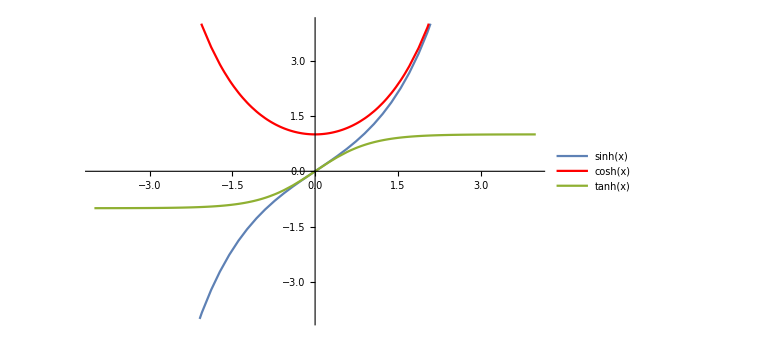
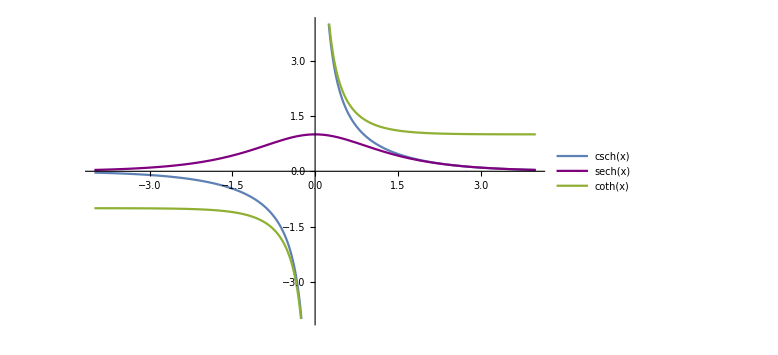

```mathematica
List[Plot[{Sinh[x],Cosh[x],Tanh[x]},{x,-4,4},PlotRange->4,ImageSize->Large,PlotLegends->"Expressions",PlotStyle->{Thick,Red,Thick,Blue,Thick,Green},Background->White,AxesStyle->Arrowheads[{-0.02,0.02}]],

Plot[{Csch[x],Sech[x],Coth[x]},{x,-4,4},PlotRange->4,ImageSize->Large,PlotStyle->{Thick,Purple,Thick,Yellow,Thick,Pink},PlotLegends->"Expressions",AxesStyle->Arrowheads[{-0.02,0.02}]]
]
```